```mathematica
ϛ[x_,n_]:=1/(2n!)Sign[x] x^n
β[x_,n_]:=∑_(k=0)^(n+1) (-1)^k Binomial[n+1,k]ϛ[x+(n+1)/2-k,n]
```

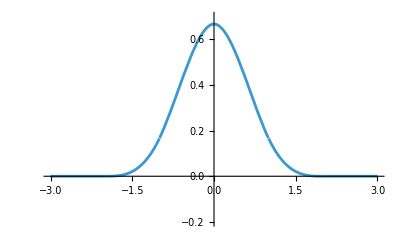

```mathematica
Plot[β[x,3],{x,-3,3},PlotRange->{{-3,3},{-0.2,0.7}}]
```

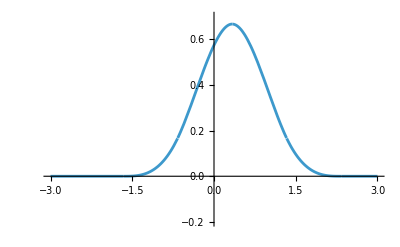

```mathematica
Plot[β[x-1/3,3],{x,-3,3},PlotRange->{{-3,3},{-0.2,0.7}}]
```

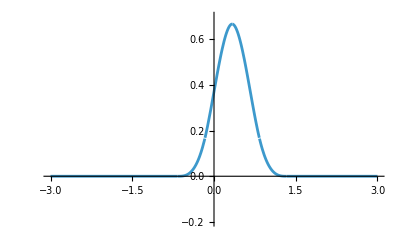

```mathematica
Plot[β[(x-1/3)/0.5,3],{x,-3,3},PlotRange->{{-3,3},{-0.2,0.7}}]
```

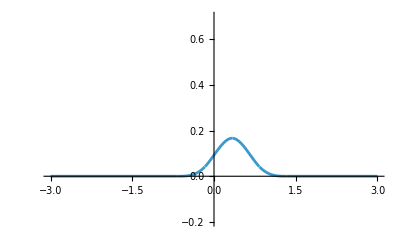

```mathematica
Plot[0.25β[(x-1/3)/0.5,3],{x,-3,3},PlotRange->{{-3,3},{-0.2,0.7}}]
```

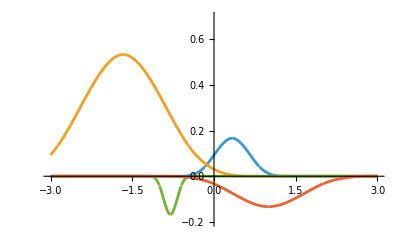

```mathematica
Plot[{0.25β[(x-1/3)/0.5,3],0.8β[(x+5/3)/1.2,3],-0.25β[(x+4/5)/0.2,3],-0.2β[(x-1)/1,3]},{x,-3,3},PlotRange->{{-3,3},{-0.2,0.7}}]
```

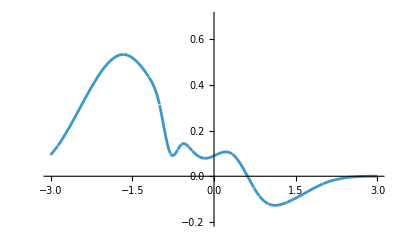

```mathematica
Plot[Total[{0.25β[(x-1/3)/0.5,3],0.8β[(x+5/3)/1.2,3],-0.25β[(x+4/5)/0.2,3],-0.2β[(x-1)/1,3]}],{x,-3,3},PlotRange->{{-3,3},{-0.2,0.7}}]
```

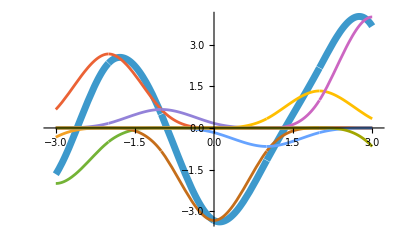

```mathematica
With[{c={-2,-3,4,1,-5,-1,2,6,-4}},Plot[{∑_(k=-4)^4 c[[k+4+(1)]]β[x-k,3],c[[-4+4+(1)]]β[x+4,3],c[[-3+4+(1)]]β[x+3,3],c[[-2+4+(1)]]β[x+2,3],c[[-1+4+(1)]]β[x+1,3],c[[0+4+(1)]]β[x,3],c[[1+4+(1)]]β[x-1,3],c[[2+4+(1)]]β[x-2,3],c[[3+4+(1)]]β[x-3,3],c[[4+4+(1)]]β[x-4,3]},{x,-3,3},PlotRange->{{-3.1,3.1},All},PlotStyle->{AbsoluteThickness[5],Medium,Medium,Medium,Medium,Medium,Medium,Medium,Medium,Medium}]]
```

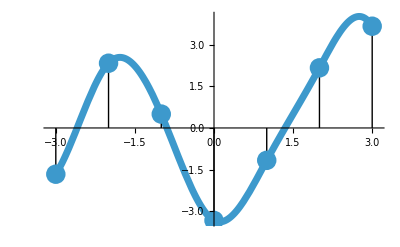

```mathematica
With[{c={-2,-3,4,1,-5,-1,2,6,-4}},Show[{Plot[∑_(k=-4)^4 c[[k+4+(1)]]β[x-k,3],{x,-3,3},PlotRange->{{-3.1,3.1},All},PlotStyle->{AbsoluteThickness[5]}],ListPlot[Table[∑_(k=-4)^4 c[[k+4+(1)]]β[q-k,3],{q,-3,3}],DataRange->{-3,3},Filling->Axis,FillingStyle->Directive[Black],PlotMarkers->{Automatic,Large}]}]]
```

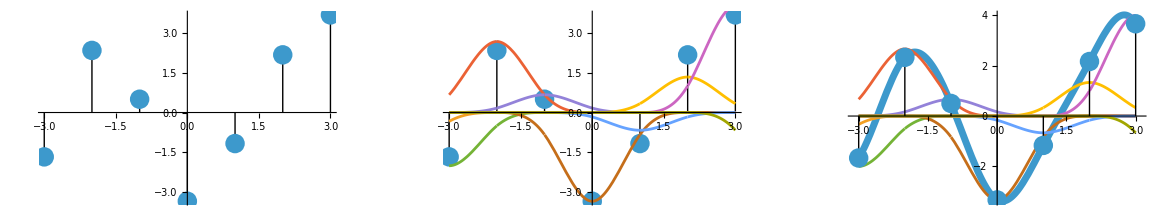

```mathematica
GraphicsRow[{With[{c={-2,-3,4,1,-5,-1,2,6,-4}},ListPlot[Table[∑_(k=-4)^4 c[[k+4+(1)]]β[q-k,3],{q,-3,3}],DataRange->{-3,3},Filling->Axis,FillingStyle->Directive[Black],PlotMarkers->{Automatic,Large}]]," \[LongRightArrow\] ",With[{c={-2,-3,4,1,-5,-1,2,6,-4}},Show[{ListPlot[Table[∑_(k=-4)^4 c[[k+4+(1)]]β[q-k,3],{q,-3,3}],DataRange->{-3,3},Filling->Axis,FillingStyle->Directive[Black],PlotMarkers->{Automatic,Large}],Plot[{Null,c[[-4+4+(1)]]β[x+4,3],c[[-3+4+(1)]]β[x+3,3],c[[-2+4+(1)]]β[x+2,3],c[[-1+4+(1)]]β[x+1,3],c[[0+4+(1)]]β[x,3],c[[1+4+(1)]]β[x-1,3],c[[2+4+(1)]]β[x-2,3],c[[3+4+(1)]]β[x-3,3],c[[4+4+(1)]]β[x-4,3]},{x,-3,3},PlotRange->{{-3.1,3.1},All},PlotStyle->{AbsoluteThickness[5],Medium,Medium,Medium,Medium,Medium,Medium,Medium,Medium,Medium}]}]]," \[LongRightArrow\] ",With[{c={-2,-3,4,1,-5,-1,2,6,-4}},Show[{Plot[{∑_(k=-4)^4 c[[k+4+(1)]]β[x-k,3],c[[-4+4+(1)]]β[x+4,3],c[[-3+4+(1)]]β[x+3,3],c[[-2+4+(1)]]β[x+2,3],c[[-1+4+(1)]]β[x+1,3],c[[0+4+(1)]]β[x,3],c[[1+4+(1)]]β[x-1,3],c[[2+4+(1)]]β[x-2,3],c[[3+4+(1)]]β[x-3,3],c[[4+4+(1)]]β[x-4,3]},{x,-3,3},PlotRange->{{-3.1,3.1},All},PlotStyle->{AbsoluteThickness[5],Medium,Medium,Medium,Medium,Medium,Medium,Medium,Medium,Medium}],ListPlot[Table[∑_(k=-4)^4 c[[k+4+(1)]]β[q-k,3],{q,-3,3}],DataRange->{-3,3},Filling->Axis,FillingStyle->Directive[Black],PlotMarkers->{Automatic,Large}]}]]},ImageSize->{360 3+40 2,224}]
```